```mathematica
<<SpinWeightedSpheroidalHarmonics`
<<KerrGeodesics`
```

```mathematica
𝔰[sp_,l_,lp_, m_]:= -sp  Sqrt[(2(2l+1))/(2 lp +1)]ClebschGordan[{l,m},{1,0},{lp,m}] ClebschGordan[{l,-sp} ,{1,sp }, {lp ,0}]
Ccoef[s_,j_,k_,m_,bs_]:=𝔰[s,j,k,m]*(j/.bs);
CLcoef [a_,m_,n_,j_,k_,ω_, bs_]:=(j/.bs)*(Sqrt[j(j+1)] KroneckerDelta[j,k] - a ω 𝔰[+1, j,k,m]);
prec=40;
l =20;
m=2;
n=3;
a= SetPrecision[0.9,prec];
p=SetPrecision[20, prec];
e=SetPrecision[0.8,prec];
x=1;
Ω =KerrGeoFrequencies[a,p,e,x];
ω[m_,n_]:=m Ω[[3]] + n Ω[[1]];
S = SpinWeightedSpheroidalHarmonicS[+1,l,m,a ω[m,n]][θ,0]
```

SpinWeightedSpheroidalHarmonicSFunction[…][θ,0]

```mathematica
D[S,θ]/.θ->0
```

0

```mathematica
C:=(D[s,θ] + m Csc[θ]s - a ω[m,n] Sin[θ] s+ Cot[θ] s)/.θ->θθ
```

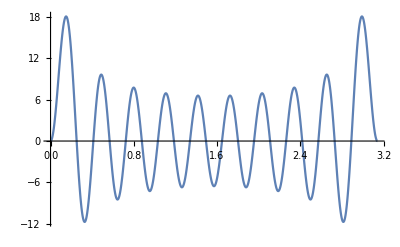

```mathematica
Plot[L1[S,t],{t,0,π}]
```

```mathematica
LMAX = 20;
```

```mathematica
L1Proj= Module[{},
bsplus = SpinWeightedSpheroidalHarmonicS[1,l,m,N[a ω[m,n]],Method->{"SphericalExpansion","NumTerms"->LMAX+1}]["ExpansionCoefficients"];
Sum[CLcoef[a,m,n,j,k,ω[m,n], bsplus]SpinWeightedSphericalHarmonicY[0,k,m,θ,0],{j,Max[1,Abs[m]],LMAX},{k,1 LMAX}]
];
```

ClebschGordan::phy: ThreeJSymbol[{2,2},{1,0},{1,-2}] is not physical.

SpinWeightedSphericalHarmonicY::params: Invalid parameters s=0, l=1, m=2

ClebschGordan::tri: ThreeJSymbol[{2,2},{1,0},{4,-2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{2,-1},{1,1},{4,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{2,2},{1,0},{5,-2}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

SpinWeightedSphericalHarmonicY::params: Invalid parameters s=0, l=1, m=2

General::stop: Further output of SpinWeightedSphericalHarmonicY::params will be suppressed during this calculation.

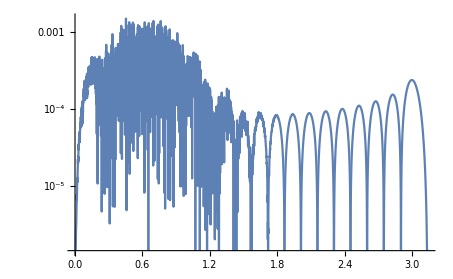

```mathematica
LogPlot[Abs[(L1Proj/.θ->t)-L1[S,t]],{t,0,π}]
```

```mathematica
SpinWeightedSphericalHarmonicY[0,1,2,θ,0]
```

SpinWeightedSphericalHarmonicY::params: Invalid parameters s=0, l=1, m=2

$Failed

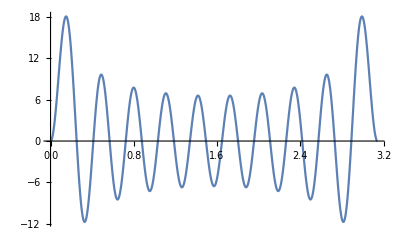

```mathematica
Plot[L1Proj,{θ,0,π}]
```